```mathematica
prob = TriangularDistribution[{6, 40}, 15]
```

TriangularDistribution[{6,40},15]

```mathematica
dist = distBall = PDF[prob, x]
```

Piecewise[{{1/153 (-6+x), 6≤x≤15}, {(40-x)/425, 15<x≤40}, {0, True}}]

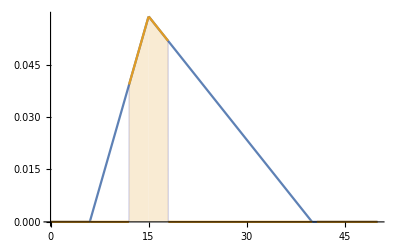

```mathematica
Plot[Evaluate[dist*{1,Boole[12<x<18]}],{x,0,50},Filling->{2->Axis}]
```

```mathematica
dist[18]
```

(Piecewise[{{1/153 (-6+x), 6≤x≤15}, {(40-x)/425, 15<x≤40}, {0, True}}])[18]

```mathematica
dist(18)
```

18 (Piecewise[{{1/153 (-6+x), 6≤x≤15}, {(40-x)/425, 15<x≤40}, {0, True}}])

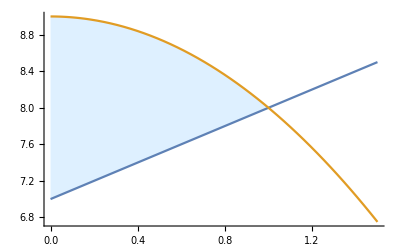

```mathematica
Plot[{x+7,9-x^2},{x,0,1.5},Filling->{1->{{2},{LightBlue,White}}}]
```

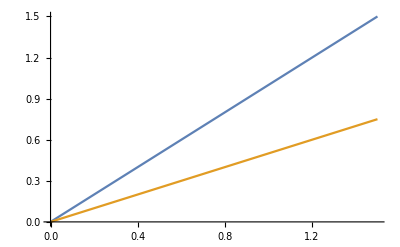

```mathematica
Plot[{x, x/2},{x,0,1.5},Filling->{1->{{2},{LightBlue,White}}}]
```

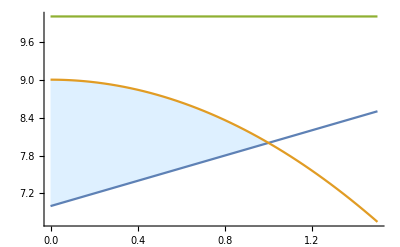

```mathematica
Plot[{x+7,9-x^2, 10},{x,0,1.5},Filling->{1->{{2},{LightBlue,White}}}]
```

```mathematica
Plot[{x+7,9-x^2},{x,0,1.5},Filling->{1->{{2},{LightBlue,White}}}]
```

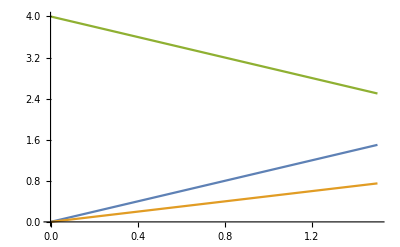

```mathematica
Plot[{x, x/2, 4 - x},{x,0,1.5},Filling->{1->{{2},{LightBlue,White}}}]
```

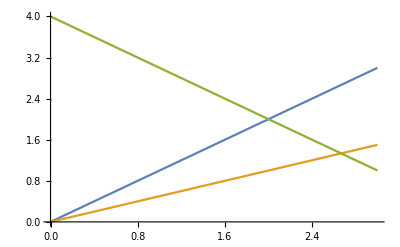

```mathematica
Plot[{x, x/2, 4 - x},{x,0,3},Filling->{1->{{2},{LightBlue,White}}}]
```

```mathematica
Plot[{x, x/2, 4 - x},{x,0,1.5},Filling->{1->{{2},{LightBlue,White, LightGray}}}]
```

-Graphics-

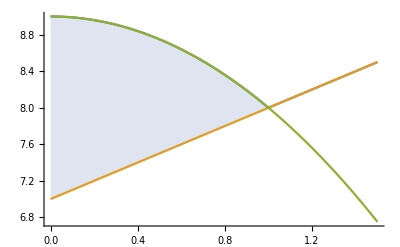

```mathematica
Plot[{Max[x+7,9-x^2],x+7,9-x^2},{x,0,1.5},Filling->{1->{2}}]
```

RegionPlot::invplotreg: {r} is not a valid region to plot.

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[List[List[], List[], List[Directive[Opacity[Skeleton[1]], RGBColor[Skeleton[3]], AbsoluteThickness[Skeleton[1]]], LineBox[List[Skeleton[62]]]], List[Directive[Opacity[Skeleton[1]], RGBColor[Skeleton[3]], AbsoluteThickness[Skeleton[1]]], LineBox[List[Skeleton[52]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

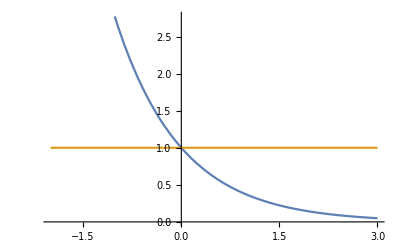
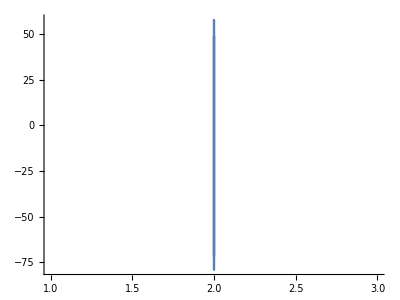
Show[{-Graphics-,-Graphics-,RegionPlot[r,ColorFunction→Rainbow]}]

```mathematica
Show[{Plot[{Exp[-x],1},{x,-2,3}],PolarPlot[2/Cos[t],{t,0,2 π}],RegionPlot[r,ColorFunction->"Rainbow"]}]
```

```mathematica
Show[{Plot[{Exp[-x],1},{x,-2,3}],PolarPlot[2/Cos[t],{t,0,2 π}],RegionPlot[r,ColorFunction->"Blue"]}]
```

RegionPlot::cfun: Value of option ColorFunction -> "Blue" is not a valid color function, or a gradient ColorData entity.

RegionPlot::invplotreg: {r} is not a valid region to plot.

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[List[List[], List[], List[Directive[Opacity[Skeleton[1]], RGBColor[Skeleton[3]], AbsoluteThickness[Skeleton[1]]], LineBox[List[Skeleton[62]]]], List[Directive[Opacity[Skeleton[1]], RGBColor[Skeleton[3]], AbsoluteThickness[Skeleton[1]]], LineBox[List[Skeleton[52]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show[{-Graphics-,-Graphics-,RegionPlot[r,ColorFunction→Blue]}]

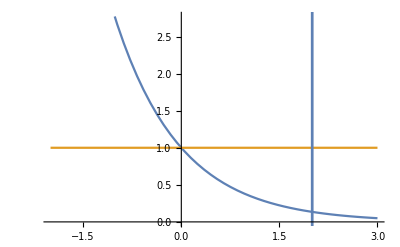

```mathematica
Show[{Plot[{Exp[-x],1},{x,-2,3}],PolarPlot[2/Cos[t],{t,0,2 π}]}]
```

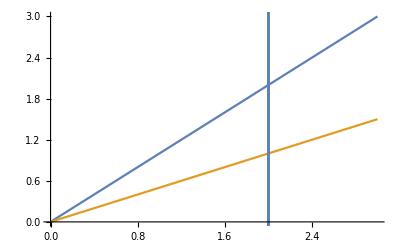

```mathematica
Show[{Plot[{x,x/2},{x,0,3}],PolarPlot[2/Cos[t],{t,0,2 π}]}]
```

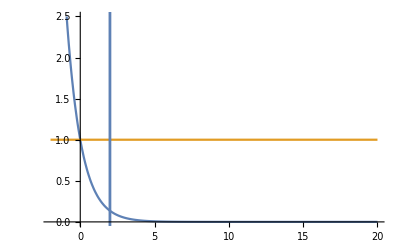

```mathematica
Show[{Plot[{Exp[-x],1},{x,-2,20}],PolarPlot[2/Cos[t],{t,0,2 π}]}]
```

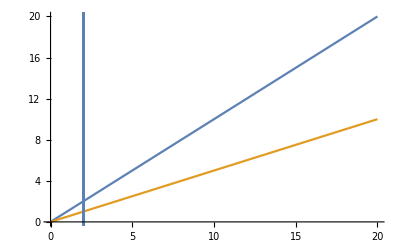

```mathematica
Show[{Plot[{x,x/2},{x,0,20}],PolarPlot[2/Cos[t],{t,0,2 π}]}]
```

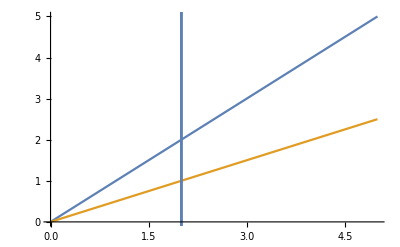

```mathematica
Show[{Plot[{x,x/2},{x,0,5}],PolarPlot[2/Cos[t],{t,0,2 π}]}]
```

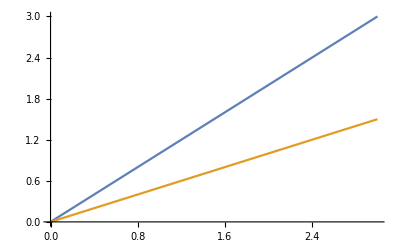

```mathematica
Show[{Plot[{x,x/2},{x,0,3}],PolarPlot[10/Cos[t],{t,0,2 π}]}]
```

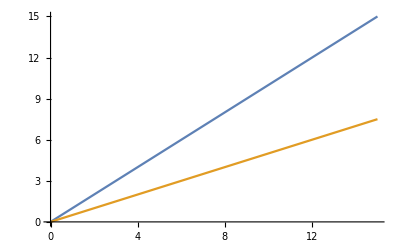
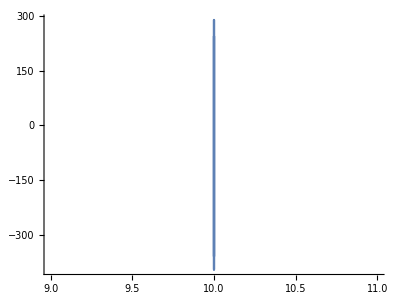
how[{-Graphics-,-Graphics-}]

```mathematica
how[{Plot[{x,x/2},{x,0,15}],PolarPlot[10/Cos[t],{t,0,2 π}]}]
```

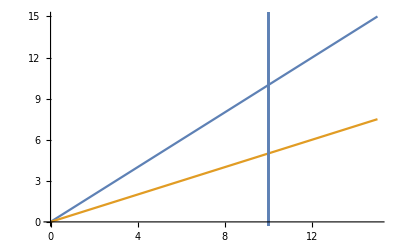

```mathematica
Show[{Plot[{x,x/2},{x,0,15}],PolarPlot[10/Cos[t],{t,0,2 π}]}]
```